```mathematica
ClearAll["Global`*"];
```

```mathematica
r[t_]:=(x=-Sin[t];y=Cos[t];{x,y});
h[x_,y_,t_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];(y-P1[[2]])*(P2[[1]]-P1[[1]])-(x-P1[[1]])*(P2[[2]]-P1[[2]]));
hd[t_]:=D[h[x_,y_,t],t];
(*Print[FullSimplify[h[x_,y_,t_]]];*)
(*Print[FullSimplify[hd[t_]]];*)
```

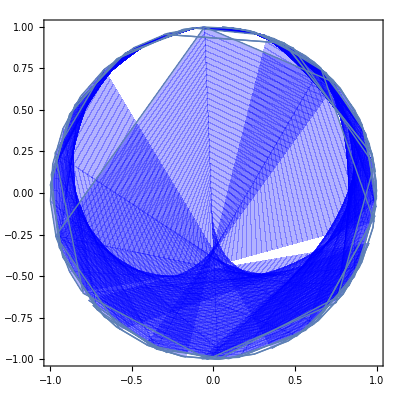

(Cos[2^(1-Floor[Log[t_]]) π t_]-Cos[2^(3-Floor[Log[4 t_]]) π t_]) x_+y_ (Sin[2^(1-Floor[Log[t_]]) π t_]-Sin[2^(3-Floor[Log[4 t_]]) π t_])-Sin[2 (2^(-Floor[Log[t_]])-2^(2-Floor[Log[4 t_]])) π t_]

```mathematica
f[n_]:=n*4;
g[n_]:=n/2^Floor[Log[n]];
parametricFunc[t_,u_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];{P1[[1]]+u*(P2[[1]]-P1[[1]]),P1[[2]]+u*(P2[[2]]-P1[[2]])});
ParametricPlot[parametricFunc[t,u],{t,0.01,1},{u,0,1},PlotStyle->Blue]
h[x_,y_,t_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];(y-P1[[2]])*(P2[[1]]-P1[[1]])-(x-P1[[1]])*(P2[[2]]-P1[[2]]));
hd[t_]:=D[h[x_,y_,t],t];
Print[FullSimplify[h[x_,y_,t_]]];
(*Print[FullSimplify[hd[t_]]];*)
```

```mathematica
g[n_]:=n/2^((Log[n]-SawtoothWave[Log[n]]));
parametricFunc[t_,u_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];{P1[[1]]+u*(P2[[1]]-P1[[1]]),P1[[2]]+u*(P2[[2]]-P1[[2]])});
ParametricPlot[parametricFunc[t,u],{t,0.01,1},{u,0,1},PlotStyle->Blue]
h[x_,y_,t_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];(y-P1[[2]])*(P2[[1]]-P1[[1]])-(x-P1[[1]])*(P2[[2]]-P1[[2]]));
hd[t_]:=D[h[x_,y_,t],t];
Print[FullSimplify[hd[t_]]];
```

-Graphics-

2 π (-2^(-Floor[Log[t_]]) (Cos[2 (2^(-Floor[Log[t_]])-2^(2-Floor[Log[4 t_]])) π t_]-Cos[2^(1-Floor[Log[t_]]) π t_] y_+x_ Sin[2^(1-Floor[Log[t_]]) π t_])+2^(2-Floor[Log[4 t_]]) (Cos[2 (2^(-Floor[Log[t_]])-2^(2-Floor[Log[4 t_]])) π t_]-Cos[2^(3-Floor[Log[4 t_]]) π t_] y_+x_ Sin[2^(3-Floor[Log[4 t_]]) π t_]))